```mathematica
(*37.1*)Style[#,Background->If[EvenQ[#]==True,Yellow,LightGray]]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(*37.2*)If[PrimeQ[#]==True,Framed[#],#]&/@Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(*37.3*)If[PrimeQ[#]==True,Labeled[Framed[#],Style[#,LightGray]],#]&/@Range[100]
```

{1,22,33,4,55,6,77,8,9,10,1111,12,1313,14,15,16,1717,18,1919,20,21,22,2323,24,25,26,27,28,2929,30,3131,32,33,34,35,36,3737,38,39,40,4141,42,4343,44,45,46,4747,48,49,50,51,52,5353,54,55,56,57,58,5959,60,6161,62,63,64,65,66,6767,68,69,70,7171,72,7373,74,75,76,77,78,7979,80,81,82,8383,84,85,86,87,88,8989,90,91,92,93,94,95,96,9797,98,99,100}

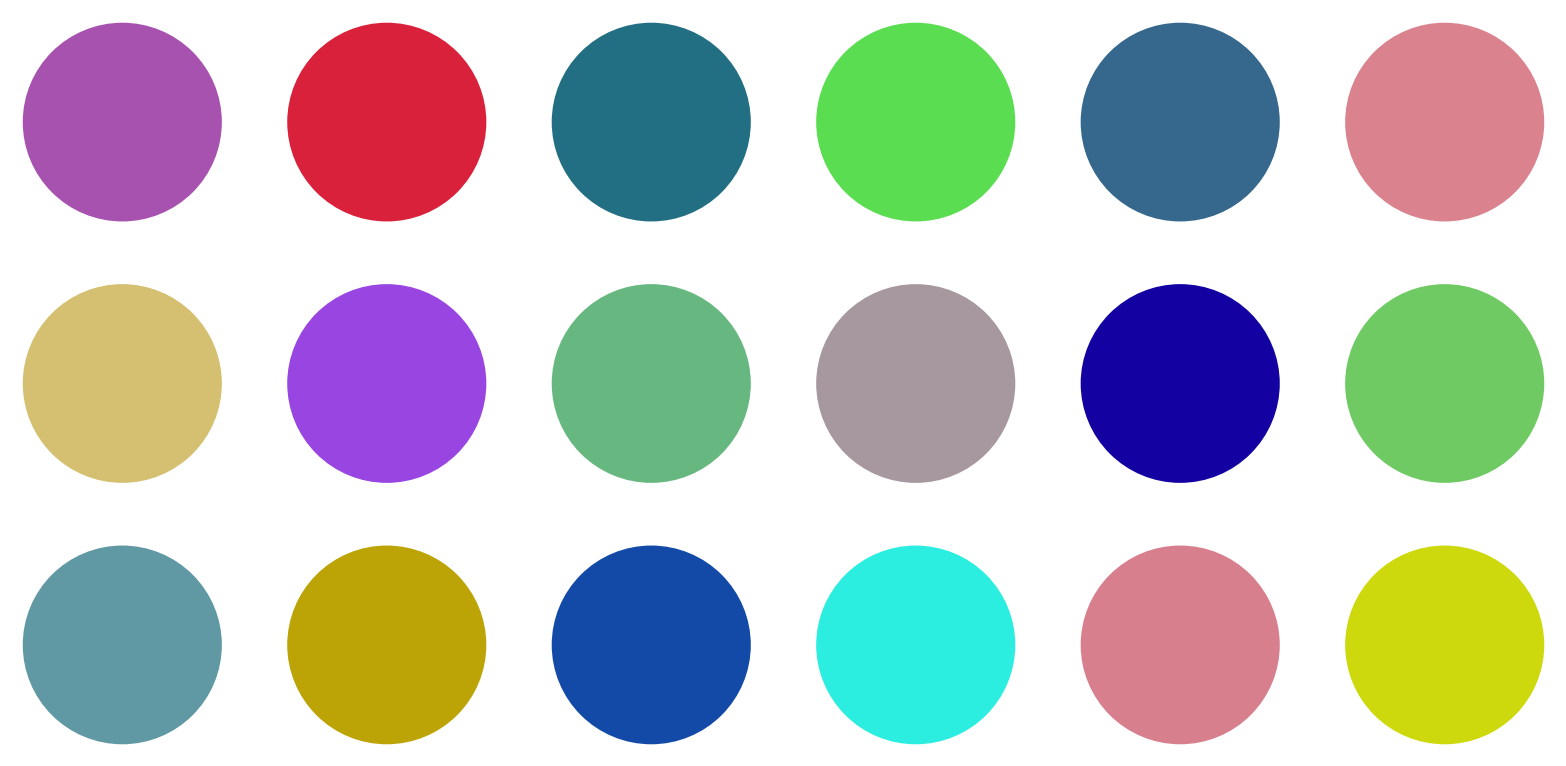

```mathematica
(*37.4*)GraphicsGrid[Table[Graphics[Style[Disk[],RandomColor[]]],3,6]]
```

```mathematica
(*37.5*)PieChart[Table[Labeled[EntityList[["GDP"]][[n]],EntityList[["Name"]][[n]]],{n,5}]]
```

-Graphics-

```mathematica
(*37.6*)PieChart[Table[Legended[EntityList[["Population"]][[n]],EntityList[["Name"]][[n]]],{n,5}]]
```

-Graphics-

```mathematica
(*37.7*)GraphicsGrid[Partition[Table[PieChart[Counts[IntegerDigits[2^n]]],{n,25}],5]]
```

-Graphics-

```mathematica
(*38.1*)Module[{x=Range[10]},x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
(*38.2*)Column[Module[{x=RandomInteger[100,10]},{x,Sort[x],Max[x],Total[x]}]]
```

{69,91,48,0,90,75,0,4,41,27}
{0,0,4,27,41,48,69,75,90,91}
91
445

```mathematica
(*38.3*)ImageCollage[Module[{x=["Image"]},{x,Blur[x],EdgeDetect[x],ColorNegate[x]}]]
```

-Graphics-

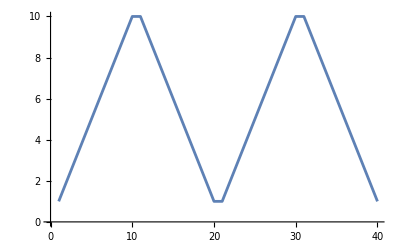

```mathematica
(*38.4*)Module[{r=Range[10]},ListLinePlot[Join[r,Reverse[r],r,Reverse[r]]]]
```

```mathematica
(*38.5*)Module[{x=Range[10]},{x+1,x-1,Reverse[x]}]
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

```mathematica
(*38.6*)NestList[Mod[17 #+2,11]&,10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
(*38.7*)Module[{vowel={a,e,i,o,u},consonant=Complement[Alphabet[],{"a","e","i","o","u"}]},Table[Riffle[RandomSample[consonant,3],RandomSample[vowel,2]],10]]
```

{{z,i,q,o,m},{m,a,d,o,s},{p,i,r,u,b},{m,a,s,o,l},{j,e,y,o,w},{g,a,k,o,j},{t,i,j,o,s},{d,e,v,i,j},{c,u,s,e,p},{c,a,g,e,j}}